```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_ada/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | ada Price | log return future | log return ada
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 1.80971 | 0.0212907 | 0.0985064
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 1.63994 | -0.0904653 | -0.214024
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 2.03132 | -0.0196938 | -0.0285262
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 2.0901 | -0.131645 | 0.0852656
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 1.91927 | 0.03685 | 0.0222558
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 1.87703 | -0.119603 | 0.0903888
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 1.71481 | -0.042369 | -0.0214709
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 1.75202 | 0.018947 | 0.0598308
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 1.65027 | -0.0359909 | 0.000674652)

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,7]]
```

log return ada

```mathematica
data[[1,6]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
{α0,β0}
```

{0.516963,-0.0281541}

```mathematica
{α0=0.5169627617935678,β0=-0.0281540975183229}
```

{0.516963,-0.0281541}

```mathematica
{α0=0.45929135433671564,β0=-0.03961855701868502}
```

{0.459291,-0.0396186}

```mathematica
For[kk=19, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,6;;7⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

19

18

17

16

15

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: 1.25331/(1.09180814843873×10^345) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMinimize::nnum: The function value √((0.466667-20. F2NIG2(«1»))^2+(0.6-10. «6»(«1»))^2+(«19»-«1»)^2+(0.333333-20. «1»)^2) is not a number at {α$375925957,β$375925957} = {28.2964,2.18771}.

14

NMinimize::nnum: The function value √((0.466667-20. F2NIG2(«1»))^2+(0.6-10. «6»(«1»))^2+(«19»-«1»)^2+(0.333333-20. «1»)^2) is not a number at {α$376372062,β$376372062} = {29.088,1.41046}.

13

12

11

10

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{2.36364,-1.89064}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_future_Tiingo_ada/

```mathematica
For[kk=0, kk≤106, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,7⟧;
rf=data2⟦2;;All,6⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.99606977107623}. NIntegrate obtained 0.127974 and 0.000193382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.99606977107623}. NIntegrate obtained 0.127386 and 0.000187802 for the integral and error estimates.

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.99606977107623}. NIntegrate obtained 0.126932 and 0.000201767 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

81

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

82

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

83

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

84

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

85

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

86

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

87

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

88

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

89

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

90

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

91

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

92

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

93

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

94

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

95

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

96

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

97

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

98

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

99

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

100

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

101

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

102

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

103

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

104

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

105

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

106

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.329801 | 0.349506 | 0.219275 | 0.200983 | 0.203611 | 0.182615
 | 2021-05-13 | 0.360042 | 0.21778 | 0.218239 | 0.198463 | 0.210064 | 0.219227
 | 2021-05-06 | 0.364869 | 0.201948 | 0.250102 | 0.197795 | 0.219461 | 0.219901
 | 2021-04-29 | 0.372613 | 0.206991 | 0.272133 | 0.202577 | 0.223694 | 0.224688
 | 2021-04-22 | 0.363436 | 0.201606 | 0.270908 | 0.198874 | 0.219728 | 0.218522
 | 2021-04-15 | 0.381188 | 0.226401 | 0.244123 | 0.209303 | 0.213104 | 0.246876
 | 2021-04-08 | 0.359944 | 0.223669 | 0.24706 | 0.205289 | 0.207619 | 0.223702
 | 2021-04-01 | 0.385117 | 0.2263 | 0.242456 | 0.209683 | 0.212828 | 0.251789
 | 2021-03-25 | 0.388909 | 0.230578 | 0.247287 | 0.212297 | 0.216113 | 0.251818
 | 2021-03-18 | 0.36106 | 0.246327 | 0.2467 | 0.220198 | 0.201094 | 0.228734
 | 2021-03-11 | 0.368252 | 0.248418 | 0.254072 | 0.222659 | 0.207025 | 0.233369
 | 2021-03-04 | 0.421486 | 0.265833 | 0.231315 | 0.23956 | 0.21996 | 0.281443
 | 2021-02-25 | 0.396084 | 0.263658 | 0.291016 | 0.245726 | 0.228452 | 0.2473
 | 2021-02-18 | 0.439231 | 0.307378 | 0.28489 | 0.262589 | 0.240481 | 0.293555
 | 2021-02-10 | 0.449182 | 0.328941 | 0.257659 | 0.317204 | 0.248703 | 0.295925
 | 2021-02-03 | 0.480158 | 0.356322 | 0.282769 | 0.346718 | 0.277242 | 0.309095
 | 2021-01-27 | 0.495773 | 0.338033 | 0.302049 | 0.325558 | 0.278839 | 0.318038
 | 2021-01-20 | 0.485997 | 0.334272 | 0.318492 | 0.293706 | 0.271909 | 0.315387
 | 2021-01-12 | 0.485889 | 0.324674 | 0.306715 | 0.284984 | 0.26197 | 0.322333
 | 2020-12-31 | 0.491151 | 0.326631 | 0.297798 | 0.309763 | 0.269224 | 0.319964
 | 2020-12-23 | 0.487298 | 0.354992 | 0.303644 | 0.334577 | 0.282352 | 0.310413
 | 2020-12-16 | 0.502649 | 0.364545 | 0.333394 | 0.3472 | 0.301766 | 0.316168
 | 2020-12-09 | 0.494133 | 0.361987 | 0.330446 | 0.341587 | 0.297672 | 0.30705
 | 2020-12-02 | 0.493099 | 0.524946 | 0.328196 | 0.354067 | 0.306841 | 0.298236
 | 2020-11-23 | 0.488645 | 0.521053 | 0.33734 | 0.328311 | 0.28911 | 0.289852
 | 2020-11-16 | 0.489475 | 0.522038 | 0.340246 | 0.329418 | 0.290985 | 0.289745
 | 2020-11-09 | 0.495138 | 0.531009 | 0.33438 | 0.348808 | 0.297488 | 0.297189
 | 2020-11-02 | 0.510941 | 0.528224 | 0.356417 | 0.335812 | 0.301877 | 0.307389
 | 2020-10-26 | 0.496275 | 0.533629 | 0.340755 | 0.352038 | 0.302712 | 0.289701
 | 2020-10-19 | 0.487149 | 0.528793 | 0.350355 | 0.34994 | 0.30077 | 0.274284
 | 2020-10-12 | 0.466519 | 0.506101 | 0.380517 | 0.336814 | 0.289507 | 0.242405
 | 2020-10-05 | 0.461521 | 0.507357 | 0.332541 | 0.328521 | 0.279088 | 0.257271
 | 2020-09-28 | 0.456143 | 0.503945 | 0.334458 | 0.326611 | 0.27806 | 0.250375
 | 2020-09-21 | 0.467431 | 0.481962 | 0.366609 | 0.311064 | 0.286179 | 0.250849
 | 2020-09-14 | 0.476691 | 0.488875 | 0.364144 | 0.314889 | 0.285523 | 0.260025
 | 2020-09-04 | 0.459856 | 0.497532 | 0.363348 | 0.315207 | 0.30638 | 0.222203
 | 2020-08-28 | 0.444631 | 0.48924 | 0.32815 | 0.300828 | 0.289178 | 0.236189
 | 2020-08-21 | 0.44867 | 0.489074 | 0.319295 | 0.297321 | 0.278896 | 0.248129
 | 2020-08-14 | 0.434759 | 0.471714 | 0.302361 | 0.282162 | 0.263145 | 0.253219
 | 2020-08-07 | 0.445734 | 0.453933 | 0.300668 | 0.274287 | 0.278991 | 0.247657
 | 2020-07-31 | 0.443929 | 0.470774 | 0.318379 | 0.290783 | 0.297933 | 0.226241
 | 2020-07-24 | 0.451045 | 0.467771 | 0.337889 | 0.286726 | 0.305266 | 0.217405
 | 2020-07-17 | 0.463256 | 0.448975 | 0.30248 | 0.276568 | 0.285285 | 0.264736
 | 2020-07-10 | 0.459001 | 0.449124 | 0.295133 | 0.275314 | 0.278381 | 0.263842
 | 2020-07-02 | 0.463102 | 0.455739 | 0.311043 | 0.286555 | 0.285046 | 0.254516
 | 2020-06-23 | 0.446884 | 0.440633 | 0.281512 | 0.270301 | 0.26881 | 0.265655
 | 2020-06-16 | 0.458628 | 0.453431 | 0.303721 | 0.279139 | 0.281793 | 0.266581
 | 2020-06-09 | 0.46021 | 0.416749 | 0.296662 | 0.266528 | 0.277561 | 0.269127
 | 2020-06-02 | 0.460425 | 0.424031 | 0.301811 | 0.267174 | 0.281148 | 0.270014
 | 2020-05-26 | 0.44913 | 0.411962 | 0.297067 | 0.262896 | 0.272531 | 0.26195
 | 2020-05-18 | 0.442583 | 0.404088 | 0.291184 | 0.261031 | 0.268731 | 0.259538
 | 2020-05-11 | 0.433495 | 0.39667 | 0.287173 | 0.258503 | 0.263407 | 0.251901
 | 2020-05-04 | 0.436126 | 0.405504 | 0.291424 | 0.258045 | 0.265483 | 0.255272
 | 2020-04-27 | 0.454649 | 0.412896 | 0.306287 | 0.270517 | 0.278662 | 0.268709
 | 2020-04-20 | 0.445972 | 0.40851 | 0.300449 | 0.265451 | 0.272819 | 0.264999
 | 2020-04-13 | 0.451314 | 0.424977 | 0.28628 | 0.26393 | 0.275008 | 0.265493
 | 2020-04-03 | 0.447061 | 0.412078 | 0.307127 | 0.265024 | 0.274933 | 0.259577
 | 2020-03-27 | 0.447948 | 0.432278 | 0.315885 | 0.267033 | 0.284602 | 0.257107
 | 2020-03-20 | 0.441275 | 0.399748 | 0.302322 | 0.263086 | 0.270628 | 0.257241
 | 2020-03-13 | 0.435123 | 0.387545 | 0.307914 | 0.2471 | 0.281251 | 0.239248
 | 2020-03-06 | 0.430808 | 0.269498 | 0.299286 | 0.181351 | 0.243476 | 0.27041
 | 2020-02-28 | 0.429726 | 0.269269 | 0.30383 | 0.171541 | 0.238657 | 0.256964
 | 2020-02-21 | 0.433699 | 0.279275 | 0.300737 | 0.175688 | 0.240953 | 0.267598
 | 2020-02-13 | 0.442983 | 0.276841 | 0.292948 | 0.178344 | 0.246425 | 0.274748
 | 2020-02-06 | 0.449366 | 0.281298 | 0.283968 | 0.188371 | 0.24511 | 0.309495
 | 2020-01-30 | 0.462197 | 0.224675 | 0.308978 | 0.176109 | 0.270462 | 0.308595
 | 2020-01-23 | 0.457438 | 0.167303 | 0.346896 | 0.14787 | 0.278858 | 0.27592
 | 2020-01-15 | 0.455262 | 0.166202 | 0.341597 | 0.148553 | 0.277162 | 0.276828
 | 2020-01-08 | 0.446305 | 0.163444 | 0.339941 | 0.143005 | 0.272742 | 0.270564
 | 2019-12-31 | 0.442062 | 0.161387 | 0.33526 | 0.141763 | 0.270834 | 0.268409
 | 2019-12-23 | 0.444187 | 0.162999 | 0.335961 | 0.143364 | 0.272246 | 0.265829
 | 2019-12-16 | 0.443764 | 0.163207 | 0.362723 | 0.14362 | 0.272207 | 0.265377
 | 2019-12-09 | 0.444177 | 0.151867 | 0.357542 | 0.14613 | 0.271632 | 0.26787
 | 2019-12-02 | 0.449643 | 0.159283 | 0.355392 | 0.147875 | 0.27234 | 0.270875
 | 2019-11-22 | 0.442142 | 0.161856 | 0.35438 | 0.147738 | 0.271554 | 0.265817
 | 2019-11-15 | 0.442882 | 0.162526 | 0.346247 | 0.150381 | 0.270673 | 0.268085
 | 2019-11-08 | 0.457808 | 0.148826 | 0.376252 | 0.144552 | 0.275613 | 0.280901
 | 2019-11-01 | 0.467515 | 0.157792 | 0.382608 | 0.147582 | 0.284073 | 0.284284
 | 2019-10-25 | 0.467227 | 0.155193 | 0.378417 | 0.152088 | 0.278978 | 0.299083
 | 2019-10-18 | 0.468745 | 0.151717 | 0.402706 | 0.150627 | 0.275679 | 0.284757
 | 2019-10-11 | 0.474135 | 0.151425 | 0.419893 | 0.152601 | 0.275724 | 0.295491
 | 2019-10-04 | 0.478763 | 0.15656 | 0.412407 | 0.155281 | 0.275164 | 0.299905
 | 2019-09-27 | 0.482574 | 0.162593 | 0.403025 | 0.154366 | 0.272333 | 0.306553
 | 2019-09-20 | 0.487934 | 0.193409 | 0.412991 | 0.0856277 | 0.270077 | 0.306663
 | 2019-09-13 | 0.489128 | 0.205374 | 0.410292 | 0.0908558 | 0.279957 | 0.300304
 | 2019-09-06 | 0.498209 | 0.215282 | 0.409553 | 0.0992747 | 0.285297 | 0.309681
 | 2019-08-29 | 0.51983 | 0.213174 | 0.420296 | 0.0983203 | 0.283432 | 0.336983
 | 2019-08-22 | 0.5332 | 0.194374 | 0.435748 | 0.115135 | 0.289858 | 0.350463
 | 2019-08-15 | 0.539376 | 0.202982 | 0.437159 | 0.116846 | 0.294469 | 0.354136
 | 2019-08-08 | 0.546982 | 0.217473 | 0.45427 | 0.126582 | 0.31036 | 0.345848
 | 2019-08-01 | 0.575982 | 0.233289 | 0.446772 | 0.14362 | 0.309942 | 0.385587
 | 2019-07-25 | 0.584224 | 0.243608 | 0.468802 | 0.148574 | 0.330648 | 0.374546
 | 2019-07-18 | 0.593499 | 0.247628 | 0.46639 | 0.155266 | 0.335165 | 0.38567
 | 2019-07-11 | 0.583506 | 0.239789 | 0.473001 | 0.149808 | 0.326865 | 0.381254
 | 2019-07-03 | 0.579447 | 0.232631 | 0.459395 | 0.145558 | 0.307685 | 0.392721
 | 2019-06-26 | 0.59843 | 0.248456 | 0.474327 | 0.150384 | 0.313585 | 0.422433
 | 2019-06-19 | 0.608562 | 0.25199 | 0.496449 | 0.155321 | 0.330743 | 0.406762
 | 2019-06-12 | 0.618807 | 0.278309 | 0.50448 | 0.227331 | 0.344079 | 0.403425
 | 2019-06-05 | 0.625871 | 0.29316 | 0.491816 | 0.240663 | 0.346958 | 0.405693
 | 2019-05-29 | 0.621135 | 0.290419 | 0.487462 | 0.234652 | 0.341365 | 0.402095
 | 2019-05-21 | 0.610808 | 0.283645 | 0.468664 | 0.236874 | 0.334218 | 0.393238
 | 2019-05-14 | 0.605781 | 0.281315 | 0.477193 | 0.231492 | 0.336195 | 0.385324
 | 2019-05-07 | 0.611833 | 0.292009 | 0.459644 | 0.25492 | 0.337875 | 0.396349
 | 2019-04-30 | 0.630127 | 0.299942 | 0.479199 | 0.270353 | 0.350277 | 0.400482
 | 2019-04-23 | 0.619786 | 0.278903 | 0.47966 | 0.242625 | 0.33749 | 0.392051
 | 2019-04-15 | 0.649304 | 0.301605 | 0.505702 | 0.267748 | 0.37064 | 0.403652
 | 2019-04-08 | 0.639659 | 0.243274 | 0.495295 | 0.349551 | 0.365544 | 0.387524

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.624598 | 0.326521 | 0.396863 | 0.356119 | 0.383308 | 0.266813
 | 2021-05-13 | 0.027902 | 0.27674 | 0.313281 | 0.278208 | 0.300794 | -1.10897
 | 2021-05-06 | -2.07775 | 1.29264 | 1.46717 | 1.24528 | 1.39082 | -1.32939
 | 2021-04-29 | 0.242969 | 0.805585 | 0.604178 | 0.830994 | 0.686389 | 0.0934109
 | 2021-04-22 | 0.791065 | 0.353057 | 0.414182 | 0.345198 | 0.38672 | 0.607781
 | 2021-04-15 | 0.769327 | 0.431786 | 0.491195 | 0.426475 | 0.458216 | -0.143817
 | 2021-04-08 | 0.674496 | -1.43266 | -1.64248 | -1.41151 | -1.51229 | 0.510909
 | 2021-04-01 | 0.322179 | 0.469985 | 0.530009 | 0.466756 | 0.504498 | -0.344539
 | 2021-03-25 | 0.133492 | -0.297565 | -0.467496 | -0.28715 | -0.388789 | 0.583282
 | 2021-03-18 | 0.498794 | 0.287414 | 0.314633 | 0.281173 | 0.289116 | 0.00859528
 | 2021-03-11 | -0.0936083 | 0.124443 | 0.136938 | 0.122582 | 0.125922 | -0.107546
 | 2021-03-04 | -0.143693 | -0.659621 | -0.714194 | -0.748501 | -0.693429 | 0.682625
 | 2021-02-25 | -0.0326432 | 0.270024 | 0.281451 | 0.267625 | 0.274811 | -0.572173
 | 2021-02-18 | 0.395741 | 0.529108 | 0.713322 | 0.698996 | 0.697864 | -0.28344
 | 2021-02-10 | 0.0584743 | -0.317916 | -0.240604 | -0.360842 | -0.29715 | 0.471201
 | 2021-02-03 | -0.30966 | -2.28772 | -1.56663 | -2.90357 | -2.20467 | -0.0412807
 | 2021-01-27 | -0.236847 | 9.30176 | 8.48838 | 9.31948 | 8.38849 | 0.4353
 | 2021-01-20 | 0.788905 | 0.497689 | 0.488098 | 0.48993 | 0.468661 | 0.47348
 | 2021-01-12 | 0.126954 | -1.13861 | -1.14734 | -1.12156 | -0.825059 | 0.117442
 | 2020-12-31 | 0.177073 | -0.934785 | -1.10158 | -1.16563 | -1.05591 | 0.302139
 | 2020-12-23 | 0.0118382 | -6.67176 | -6.03194 | -7.68976 | -6.62194 | 0.44586
 | 2020-12-16 | -0.0739074 | -0.262459 | -0.199933 | -0.39972 | -0.26087 | 1.12127
 | 2020-12-09 | 0.820013 | 0.0245575 | 0.0232743 | -0.127149 | 0.0246577 | 0.717306
 | 2020-12-02 | 0.39209 | 0.290666 | 0.276639 | 0.365592 | 0.318395 | -0.0347252
 | 2020-11-23 | 0.850578 | 0.694428 | 0.69143 | 0.709442 | 0.687726 | 0.482074
 | 2020-11-16 | -0.195016 | 0.0767085 | 0.0750035 | 0.077922 | 0.0754303 | -0.0279652
 | 2020-11-09 | -1.69521 | -0.910809 | -0.843714 | -1.06855 | -0.922281 | 0.128658
 | 2020-11-02 | 0.0258561 | -2.76198 | -2.40923 | -2.7076 | -2.53372 | 0.288244
 | 2020-10-26 | 0.743219 | 0.261929 | 0.267473 | 0.180052 | 0.257976 | 1.58983
 | 2020-10-19 | 0.427379 | -0.281116 | -0.263569 | -0.330236 | -0.284839 | 0.802434
 | 2020-10-12 | 0.636573 | 0.253501 | 0.24172 | 0.249646 | 0.239954 | 0.511821
 | 2020-10-05 | 0.635497 | 0.40707 | 0.371101 | 0.416913 | 0.387275 | 0.419158
 | 2020-09-28 | 0.476788 | 0.173681 | 0.159534 | 0.180291 | 0.165252 | 0.555937
 | 2020-09-21 | 0.225476 | 0.405893 | 0.392415 | 0.392767 | 0.375513 | 0.0813918
 | 2020-09-14 | 0.400492 | 0.303997 | 0.293048 | 0.287113 | 0.265317 | -0.189818
 | 2020-09-04 | 0.570926 | 0.376507 | 0.437698 | 0.376253 | 0.398565 | 0.334291
 | 2020-08-28 | 0.408331 | 0.45123 | 0.556125 | 0.507478 | 0.553713 | 0.123602
 | 2020-08-21 | 0.511818 | 0.26213 | 0.287492 | 0.255959 | 0.282224 | 0.300221
 | 2020-08-14 | 0.768535 | 0.309053 | 0.343931 | 0.341501 | 0.342339 | 0.780257
 | 2020-08-07 | 0.485272 | -0.11184 | -0.152956 | -0.105938 | -0.112426 | 0.537935
 | 2020-07-31 | -0.113664 | 0.412211 | 0.361401 | 0.418865 | 0.364248 | -0.255283
 | 2020-07-24 | 0.774147 | -0.430955 | -0.526686 | -0.470823 | -0.524096 | 0.639654
 | 2020-07-17 | 0.492478 | -0.0104491 | -0.0118553 | -0.0102417 | -0.0105417 | 0.480445
 | 2020-07-10 | 0.10416 | 0.138802 | 0.174042 | 0.148271 | 0.156658 | 0.00489304
 | 2020-07-02 | 0.180297 | 0.185126 | 0.236437 | 0.183308 | 0.209632 | 0.0685235
 | 2020-06-23 | 0.247488 | 0.468907 | 0.476539 | 0.448491 | 0.471681 | 0.0264376
 | 2020-06-16 | -0.0147488 | 0.474925 | 0.603205 | 0.468057 | 0.539083 | -0.354129
 | 2020-06-09 | 0.649986 | 0.518663 | 0.500594 | 0.529217 | 0.515427 | 0.325488
 | 2020-06-02 | 0.259063 | 0.178489 | 0.239488 | 0.17717 | 0.214176 | 0.0976637
 | 2020-05-26 | 0.119496 | 0.23514 | 0.276788 | 0.197786 | 0.24731 | 0.0696514
 | 2020-05-18 | 0.569138 | 0.503588 | 0.639191 | 0.450912 | 0.53552 | 0.087242
 | 2020-05-11 | -0.0534771 | -1.77266 | -2.69881 | -1.8854 | -2.35767 | 0.29836
 | 2020-05-04 | 0.7258 | 0.7018 | 0.476527 | 0.699116 | 0.58862 | 0.140401
 | 2020-04-27 | 0.551745 | -0.182476 | -0.267166 | -0.193208 | -0.224487 | 0.598979
 | 2020-04-20 | 0.641335 | 0.295114 | 0.45364 | 0.312564 | 0.365936 | 0.426765
 | 2020-04-13 | 0.855603 | 0.978511 | 0.493949 | 1.03013 | 0.900881 | 0.561885
 | 2020-04-03 | 0.867081 | 0.594992 | 0.752694 | 0.526997 | 0.62384 | 0.66434
 | 2020-03-27 | 0.90431 | 1.28311 | 0.835059 | 1.26128 | 1.2072 | 0.608528
 | 2020-03-20 | 0.691141 | 0.277769 | 0.183456 | 0.290942 | 0.251198 | 0.73065
 | 2020-03-13 | 0.85371 | 0.544986 | 0.618472 | 0.462641 | 0.555472 | 0.620665
 | 2020-03-06 | 0.841086 | 0.500173 | 0.642445 | 0.481923 | 0.580742 | 0.189525
 | 2020-02-28 | 0.767868 | 0.256468 | 0.264799 | 0.255319 | 0.261236 | 0.582426
 | 2020-02-21 | 0.517607 | 0.296399 | 0.397651 | 0.273851 | 0.335421 | 0.127363
 | 2020-02-13 | 0.472084 | 0.147284 | 0.197238 | 0.136839 | 0.172789 | 0.607929
 | 2020-02-06 | 0.271503 | 0.666744 | 0.572592 | 0.659157 | 0.654323 | 0.148244
 | 2020-01-30 | 0.384127 | 0.195829 | 0.261211 | 0.175215 | 0.240058 | 0.05066
 | 2020-01-23 | -0.106805 | 0.512981 | 0.78548 | 0.481338 | 0.70284 | 0.124968
 | 2020-01-15 | 0.445489 | 0.322647 | 0.480153 | 0.308496 | 0.438333 | 0.121031
 | 2020-01-08 | 0.817516 | 1.17897 | 0.920245 | 1.19226 | 0.986521 | 0.532255
 | 2019-12-31 | 0.179646 | -0.0108105 | -0.883216 | 0.0238868 | -0.655104 | 0.332821
 | 2019-12-23 | -0.260884 | -0.0167009 | -0.0255232 | -0.0159332 | -0.0231283 | -0.874965
 | 2019-12-16 | 0.823444 | 0.285687 | 0.458503 | 0.270941 | 0.395335 | 0.741499
 | 2019-12-09 | 0.718289 | 0.418729 | 0.508603 | 0.331599 | 0.462724 | 0.41762
 | 2019-12-02 | 0.720747 | 0.492707 | 0.39039 | 0.549125 | 0.458808 | 0.799819
 | 2019-11-22 | 0.808505 | 0.380974 | 0.568642 | 0.366874 | 0.504564 | 0.551259
 | 2019-11-15 | -0.309925 | 0.277983 | 0.277983 | 0.277983 | 0.277983 | -4.23713
 | 2019-11-08 | -0.528809 | 0.539869 | 0.732877 | 0.438068 | 0.64776 | -0.913874
 | 2019-11-01 | 0.304505 | 0.398049 | 0.463991 | 0.335235 | 0.427606 | -0.246283
 | 2019-10-25 | 0.735558 | 0.10919 | -0.806603 | 0.119155 | 0.0260313 | 0.799734
 | 2019-10-18 | 0.770836 | 0.829446 | 0.301491 | 0.685638 | 0.687206 | 0.608697
 | 2019-10-11 | 0.580222 | 0.271946 | 0.420571 | 0.216037 | 0.31821 | 0.0504425
 | 2019-10-04 | 0.68944 | 0.590455 | 0.228653 | 0.517834 | 0.660191 | 0.357664
 | 2019-09-27 | 0.167569 | 0.338058 | 0.383408 | 0.26042 | 0.350269 | 0.0885603
 | 2019-09-20 | 0.729625 | 0.351411 | 0.597833 | 0.277792 | 0.476284 | -0.103024
 | 2019-09-13 | -0.0131321 | -0.0516593 | -0.0795754 | -0.0391303 | -0.0639446 | 0.103458
 | 2019-09-06 | -0.00180346 | -0.122138 | -0.170382 | -0.0893527 | -0.138866 | -0.118112
 | 2019-08-29 | -2.70424 | -0.453119 | -2.16943 | 0.0375854 | -1.23325 | 0.734622
 | 2019-08-22 | 0.723525 | 0.455915 | 0.60384 | 0.342141 | 0.609391 | -1.13948
 | 2019-08-15 | 0.183329 | 0.0646316 | -0.274355 | 0.201496 | -0.0899386 | 0.262621
 | 2019-08-08 | -0.202075 | 0.220186 | 0.143973 | 0.259318 | 0.179944 | -0.487954
 | 2019-08-01 | -4.49063 | -0.789723 | -1.64845 | -0.432798 | -1.182 | 5.00901
 | 2019-07-25 | -0.937152 | -0.772714 | -1.26894 | -0.606109 | -1.01846 | 0.198594
 | 2019-07-18 | 0.0660645 | 0.182976 | 0.182976 | 0.182976 | 0.182976 | -0.273326
 | 2019-07-11 | 0.666405 | 0.335366 | 0.486706 | 0.24941 | 0.39892 | 0.0946509
 | 2019-07-03 | 0.783231 | 0.371126 | 0.137181 | 0.305911 | 0.33963 | 1.79993
 | 2019-06-26 | -2.77691 | 0.517168 | 0.143084 | 0.648018 | 0.300904 | -15.6704
 | 2019-06-19 | -0.448589 | -1.06917 | -3.37067 | -0.720506 | -2.42248 | 1.35312
 | 2019-06-12 | 0.453288 | -0.411883 | -0.665353 | -0.398139 | -0.469572 | 0.953889
 | 2019-06-05 | 0.633509 | 0.762521 | 0.848134 | 0.675955 | 0.798151 | 0.139863
 | 2019-05-29 | 0.802922 | 0.791163 | 0.819956 | 0.705826 | 0.805982 | 0.194439
 | 2019-05-21 | 0.882811 | 0.31558 | 0.393528 | 0.291562 | 0.328194 | 0.770731
 | 2019-05-14 | 0.784467 | 0.796539 | 0.564687 | 0.720107 | 0.778 | 0.53066
 | 2019-05-07 | 0.333608 | -0.479386 | -1.08876 | -0.436407 | -0.520384 | 0.653159
 | 2019-04-30 | 0.155725 | -0.426887 | -0.558149 | -0.395242 | -0.508331 | 0.910197
 | 2019-04-23 | 0.70413 | 0.561212 | 0.523789 | 0.571899 | 0.545916 | 0.24301
 | 2019-04-15 | -0.27832 | -0.279312 | -0.372437 | -0.257585 | -0.345284 | 1.48848
 | 2019-04-08 | 0.858739 | 0.654237 | 0.653723 | 0.654781 | 0.656755 | 0.60294

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

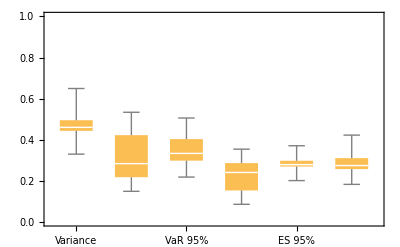

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

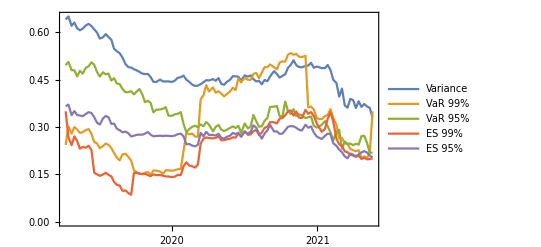

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

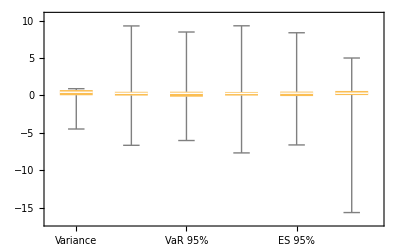

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

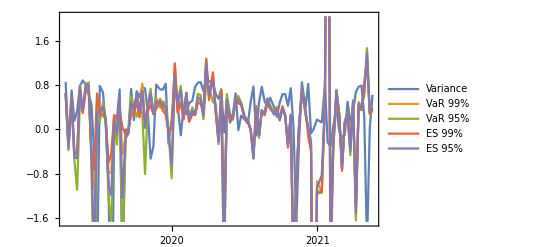

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,7]]
```

log return ada

```mathematica
data[[1,6]]
```

log return future

```mathematica
data[[2,2]]
```

2019-04-08 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤106, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | ada Price | log return future | log return ada
535 | 2019-04-08 20:00:00+00:00 | 5210. | BTCK19 Curncy | 0.08561 | 0.0381464 | -0.04533
536 | 2019-04-05 20:00:00+00:00 | 5015. | BTCK19 Curncy | 0.08958 | 0.0365523 | 0.0777383
537 | 2019-04-04 20:00:00+00:00 | 4835. | BTCK19 Curncy | 0.08288 | -0.061172 | -0.16594
538 | 2019-04-03 20:00:00+00:00 | 5140. | BTCK19 Curncy | 0.09784 | 0.0747068 | 0.177468
539 | 2019-04-02 20:00:00+00:00 | 4770. | BTCK19 Curncy | 0.08193 | 0.14528 | 0.138969
540 | 2019-04-01 20:00:00+00:00 | 4125. | BTCK19 Curncy | 0.0713 | 0.0121953 | 0.000879438
541 | 2019-03-29 20:00:00+00:00 | 4075. | BTCK19 Curncy | 0.0712373 | 0.0173272 | 0.0778784
542 | 2019-03-28 20:00:00+00:00 | 4005. | BTCJ19 Curncy | 0.0659 | 0. | -0.0248812
543 | 2019-03-27 20:00:00+00:00 | 4005. | BTCJ19 Curncy | 0.0675602 | 0.0252858 | 0.108318)

```mathematica
hvec
```

{{2019-04-08},{1.35091},{1.36196},{1.38221},{1.34051},{1.26271},{1.29452},{{0.14673702337367334, {h$443710742 -> 1.3619620416458036}},{0.07284589760138302, {h$443710742 -> 1.3822115827030765}},{0.20123072400960682, {h$443710742 -> 1.340510395340291}},{0.12154068378805231, {h$443710742 -> 1.2627086446361075}},{0.07097941588696723, {h$443710742 -> 1.2945152874644579}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤106, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤106, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=106, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤106, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

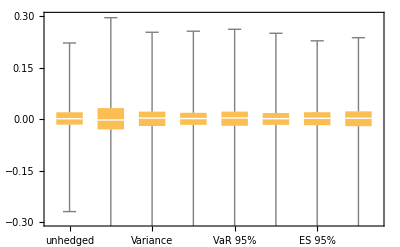

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

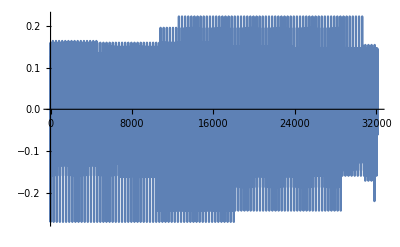

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤106, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

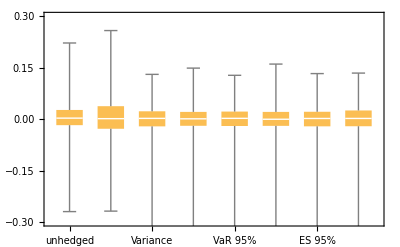

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

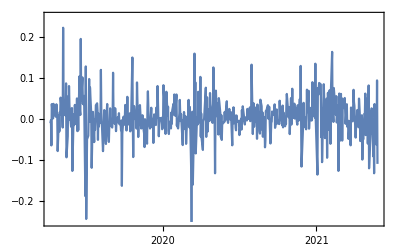
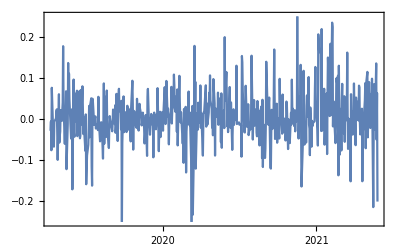

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

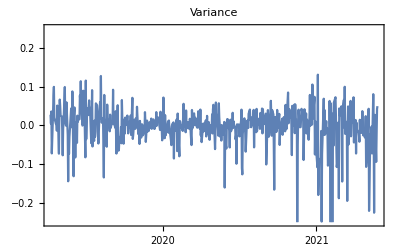
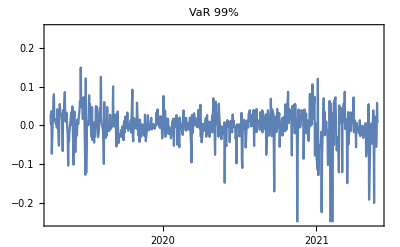
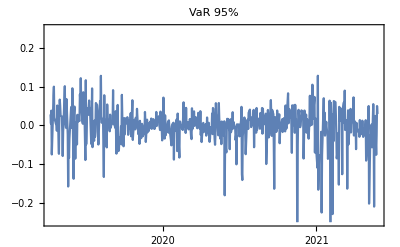
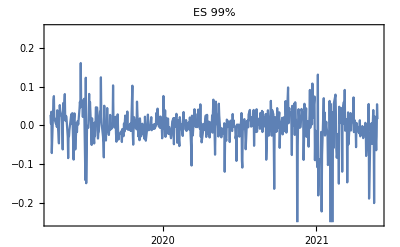
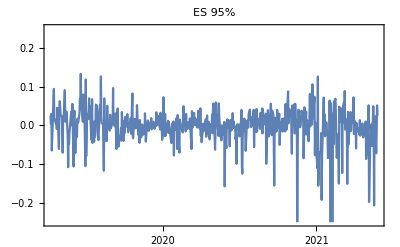
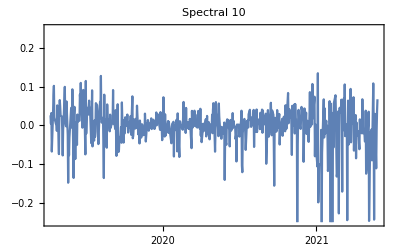

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤106, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

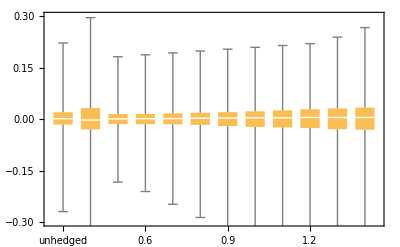

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤106, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

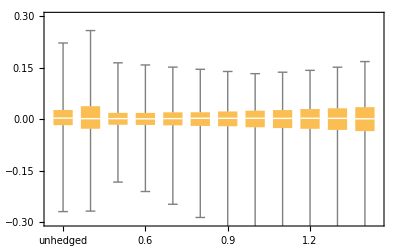

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤106, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.846885 | 0.601831 | 0.731483 | 0.656384 | 0.706498 | 0.950933
2021-05-13 | 0.884 | 0.654716 | 0.741165 | 0.658189 | 0.711623 | 1.04294
2021-05-06 | 0.904019 | 0.65506 | 0.743505 | 0.631058 | 0.704811 | 1.1211
2021-04-29 | 0.918227 | 0.647046 | 0.755599 | 0.633351 | 0.711289 | 1.09212
2021-04-22 | 0.909473 | 0.643197 | 0.754555 | 0.62888 | 0.704525 | 1.12355
2021-04-15 | 0.934834 | 0.663024 | 0.754249 | 0.654869 | 0.703608 | 1.16527
2021-04-08 | 0.90952 | 0.660215 | 0.756908 | 0.65047 | 0.696912 | 1.13943
2021-04-01 | 0.942289 | 0.663264 | 0.747973 | 0.658707 | 0.71197 | 1.15438
2021-03-25 | 0.947184 | 0.66732 | 0.7567 | 0.661842 | 0.715301 | 1.16644
2021-03-18 | 0.903313 | 0.683516 | 0.748246 | 0.668674 | 0.687564 | 1.14236
2021-03-11 | 0.90458 | 0.685666 | 0.754514 | 0.675413 | 0.693814 | 1.13159
2021-03-04 | 0.966172 | 0.704829 | 0.763143 | 0.799801 | 0.740955 | 1.09083
2021-02-25 | 0.938405 | 0.701966 | 0.755048 | 0.690824 | 0.724202 | 1.18638
2021-02-18 | 0.987485 | 0.574265 | 0.774201 | 0.758652 | 0.757424 | 1.21681
2021-02-10 | 0.998269 | 0.99472 | 0.752822 | 1.12903 | 0.929748 | 1.09684
2021-02-03 | 1.00592 | 1.02329 | 0.830744 | 1.18773 | 1.00111 | 1.09209
2021-01-27 | 1.019 | 1.00906 | 0.920827 | 1.01099 | 0.90999 | 1.09607
2021-01-20 | 1.01266 | 0.936681 | 0.897571 | 0.905039 | 0.818304 | 1.09209
2021-01-12 | 1.00561 | 0.927528 | 0.930479 | 0.921762 | 0.821504 | 1.10464
2020-12-31 | 0.983834 | 0.792324 | 0.933702 | 0.987992 | 0.894989 | 1.05248
2020-12-23 | 0.99066 | 1.02151 | 0.930178 | 1.16683 | 1.0144 | 1.04706
2020-12-16 | 1.00481 | 1.03831 | 0.9775 | 1.17181 | 1.03677 | 1.09799
2020-12-09 | 1.00029 | 1.02942 | 0.975629 | 1.15881 | 1.03362 | 1.04915
2020-12-02 | 1.00587 | 0.997168 | 0.949044 | 1.25421 | 1.09229 | 1.04298
2020-11-23 | 1.00914 | 0.986238 | 0.98198 | 1.00756 | 0.976721 | 1.04364
2020-11-16 | 0.977952 | 0.990868 | 0.968844 | 1.00654 | 0.974356 | 0.966752
2020-11-09 | 0.973383 | 1.00076 | 0.927039 | 1.17105 | 1.01337 | 1.00833
2020-11-02 | 0.989007 | 0.996698 | 0.935086 | 0.9872 | 0.95683 | 0.984809
2020-10-26 | 0.976553 | 1.0084 | 0.997413 | 1.17065 | 1.01623 | 0.976657
2020-10-19 | 0.966689 | 0.997528 | 0.935264 | 1.17183 | 1.01074 | 0.947747
2020-10-12 | 0.934488 | 0.964729 | 0.821121 | 0.917734 | 0.799585 | 0.974062
2020-10-05 | 0.923567 | 0.968799 | 0.883195 | 0.992224 | 0.921689 | 0.913443
2020-09-28 | 0.912945 | 0.965263 | 0.886639 | 1.002 | 0.918418 | 0.906283
2020-09-21 | 0.908999 | 0.929221 | 0.898366 | 0.899171 | 0.859671 | 0.861772
2020-09-14 | 0.907213 | 0.959804 | 0.925235 | 0.906494 | 0.837678 | 0.859595
2020-09-04 | 0.822554 | 0.749615 | 0.871444 | 0.749109 | 0.793531 | 0.818025
2020-08-28 | 0.774452 | 0.622824 | 0.767608 | 0.700462 | 0.764278 | 0.76341
2020-08-21 | 0.767109 | 0.713347 | 0.782366 | 0.696554 | 0.768029 | 0.735438
2020-08-14 | 0.757247 | 0.688027 | 0.765674 | 0.760264 | 0.76213 | 0.733114
2020-08-07 | 0.774511 | 0.75859 | 0.84944 | 0.74555 | 0.759886 | 0.722249
2020-07-31 | 0.775927 | 0.703881 | 0.769331 | 0.69531 | 0.765663 | 0.753417
2020-07-24 | 0.785634 | 0.687594 | 0.771399 | 0.722496 | 0.769132 | 0.747257
2020-07-17 | 0.782728 | 0.749657 | 0.850542 | 0.73478 | 0.756305 | 0.750067
2020-07-10 | 0.775462 | 0.655078 | 0.846748 | 0.706577 | 0.752197 | 0.724841
2020-07-02 | 0.762787 | 0.664726 | 0.848968 | 0.658197 | 0.75272 | 0.729414
2020-06-23 | 0.745127 | 0.739305 | 0.754999 | 0.697328 | 0.745009 | 0.706514
2020-06-16 | 0.75696 | 0.661728 | 0.840465 | 0.652159 | 0.751121 | 0.719405
2020-06-09 | 0.773661 | 0.609151 | 0.831786 | 0.655036 | 0.740195 | 0.744044
2020-06-02 | 0.777512 | 0.618478 | 0.829844 | 0.613909 | 0.742136 | 0.745679
2020-05-26 | 0.752468 | 0.704098 | 0.828809 | 0.592247 | 0.740542 | 0.67558
2020-05-18 | 0.746266 | 0.693954 | 0.880817 | 0.621365 | 0.737957 | 0.675124
2020-05-11 | 0.742025 | 0.57857 | 0.826063 | 0.608698 | 0.7349 | 0.676891
2020-05-04 | 0.753525 | 0.591455 | 0.878755 | 0.594878 | 0.735799 | 0.680293
2020-04-27 | 0.778352 | 0.604918 | 0.885672 | 0.640498 | 0.744188 | 0.734451
2020-04-20 | 0.766728 | 0.595839 | 0.883892 | 0.631071 | 0.73883 | 0.73955
2020-04-13 | 0.775087 | 0.719877 | 0.884809 | 0.702306 | 0.7463 | 0.778341
2020-04-03 | 0.775113 | 0.704907 | 0.891743 | 0.624352 | 0.739085 | 0.738613
2020-03-27 | 0.780644 | 0.630506 | 0.830881 | 0.614302 | 0.743014 | 0.755662
2020-03-20 | 0.777573 | 0.692437 | 0.880936 | 0.66611 | 0.745545 | 0.75519
2020-03-13 | 0.781617 | 0.786748 | 0.892832 | 0.667873 | 0.801885 | 0.688483
2020-03-06 | 0.793606 | 0.616452 | 0.856154 | 0.585704 | 0.752196 | 0.761582
2020-02-28 | 0.799663 | 0.615803 | 0.839592 | 0.584931 | 0.743872 | 0.819557
2020-02-21 | 0.800819 | 0.640214 | 0.858917 | 0.591511 | 0.7245 | 0.857466
2020-02-13 | 0.809748 | 0.634434 | 0.849614 | 0.589444 | 0.744298 | 0.860467
2020-02-06 | 0.813215 | 0.617709 | 0.840604 | 0.591511 | 0.734384 | 0.827597
2020-01-30 | 0.824572 | 0.617504 | 0.823672 | 0.552505 | 0.756971 | 0.83246
2020-01-23 | 0.811961 | 0.544759 | 0.834139 | 0.511156 | 0.74638 | 0.77031
2020-01-15 | 0.808542 | 0.547522 | 0.814805 | 0.523508 | 0.743838 | 0.75161
2020-01-08 | 0.801555 | 0.522997 | 0.813544 | 0.508073 | 0.739117 | 0.75921
2019-12-31 | 0.802532 | 0.518199 | 0.813995 | 0.506435 | 0.736652 | 0.750407
2019-12-23 | 0.805808 | 0.532659 | 0.81404 | 0.508174 | 0.737657 | 0.78226
2019-12-16 | 0.8087 | 0.535832 | 0.859962 | 0.508174 | 0.741485 | 0.693846
2019-12-09 | 0.809571 | 0.67205 | 0.816294 | 0.532207 | 0.74266 | 0.798807
2019-12-02 | 0.820744 | 0.665267 | 0.814243 | 0.528043 | 0.74772 | 0.772616
2019-11-22 | 0.822629 | 0.570162 | 0.851026 | 0.549061 | 0.755128 | 0.737182
2019-11-15 | 0.828688 | 0.665618 | 0.841741 | 0.542 | 0.756822 | 0.736294
2019-11-08 | 0.852975 | 0.653791 | 0.992219 | 0.530507 | 0.784448 | 0.856843
2019-11-01 | 0.86612 | 0.737263 | 0.8594 | 0.62092 | 0.792008 | 0.833062
2019-10-25 | 0.871781 | 0.652743 | 0.981463 | 0.596893 | 0.784759 | 0.812311
2019-10-18 | 0.900085 | 0.666866 | 0.968117 | 0.551246 | 0.777649 | 0.858007
2019-10-11 | 0.905729 | 0.662015 | 1.02382 | 0.525912 | 0.774636 | 0.879436
2019-10-04 | 0.913226 | 0.671761 | 1.04408 | 0.589141 | 0.795585 | 0.832914
2019-09-27 | 0.918586 | 0.768066 | 1.02926 | 0.591673 | 0.79581 | 0.87088
2019-09-20 | 0.925095 | 0.579943 | 0.986621 | 0.458447 | 0.786025 | 0.897224
2019-09-13 | 0.946505 | 0.62464 | 0.962188 | 0.473146 | 0.773188 | 0.999042
2019-09-06 | 0.955807 | 0.687471 | 0.959023 | 0.502935 | 0.781628 | 1.04409
2019-08-29 | 0.984755 | 0.585648 | 1.03264 | 0.45785 | 0.788823 | 1.02185
2019-08-22 | 1.00374 | 0.577521 | 1.00329 | 0.4334 | 0.771934 | 1.00841
2019-08-15 | 1.01078 | 0.634137 | 1.03407 | 0.472665 | 0.816498 | 1.04428
2019-08-08 | 1.02083 | 0.678566 | 1.00849 | 0.509163 | 0.852776 | 1.03497
2019-08-01 | 1.0573 | 0.737135 | 1.12298 | 0.576758 | 0.913395 | 1.08279
2019-07-25 | 1.0706 | 0.724409 | 1.11469 | 0.593374 | 0.917687 | 1.09564
2019-07-18 | 1.08101 | 0.755851 | 1.09352 | 0.611361 | 0.927034 | 1.1285
2019-07-11 | 1.09012 | 0.773993 | 1.12327 | 0.575615 | 0.92067 | 1.08685
2019-07-03 | 1.09826 | 0.668435 | 1.10702 | 0.550977 | 0.924774 | 1.11786
2019-06-26 | 1.23294 | 0.685733 | 1.14704 | 0.524373 | 0.952422 | 1.32769
2019-06-19 | 1.29169 | 0.746163 | 1.17189 | 0.559063 | 0.996497 | 1.35684
2019-06-12 | 1.32869 | 0.971488 | 1.39619 | 0.939073 | 1.10756 | 1.38973
2019-06-05 | 1.33577 | 1.0821 | 1.39135 | 0.959254 | 1.13266 | 1.40746
2019-05-29 | 1.33719 | 1.07285 | 1.39373 | 0.957129 | 1.11627 | 1.37495
2019-05-21 | 1.31962 | 1.05917 | 1.40542 | 0.95248 | 1.1152 | 1.35131
2019-05-14 | 1.30787 | 1.06343 | 1.38731 | 0.943978 | 1.08933 | 1.33013
2019-05-07 | 1.32061 | 1.07443 | 1.36168 | 0.978102 | 1.16632 | 1.329
2019-04-30 | 1.30328 | 0.994868 | 1.30078 | 0.921119 | 1.18467 | 1.26661
2019-04-23 | 1.28869 | 0.97867 | 1.29442 | 0.888495 | 1.10773 | 1.30606
2019-04-15 | 1.32311 | 0.998759 | 1.33176 | 0.921068 | 1.23466 | 1.36792
2019-04-08 | 1.35091 | 1.36196 | 1.38221 | 1.34051 | 1.26271 | 1.29452)

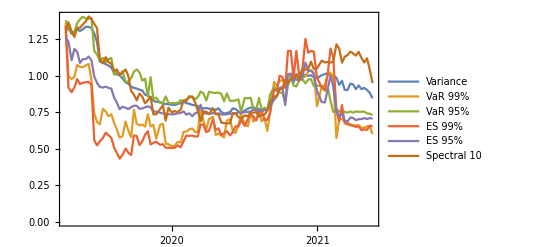

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```